```mathematica
ω=1;
F[t_]:=ⅇ^(I ω t)
```

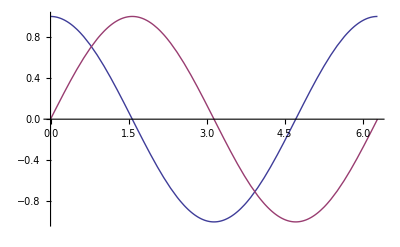

```mathematica
Plot[{Re[F[x]],Im[F[x]]},{x,0,2π}]
```

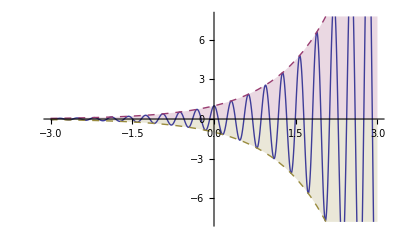

```mathematica
Plot[{E^(t) Cos[20t],E^(t),-E^(t)},{t,-3,3},Filling->{2->Axis,3->Axis},PlotStyle->{,Dashed,Dashed}]
```

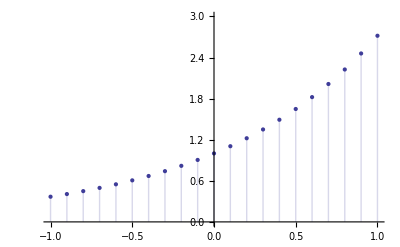

```mathematica
ListPlot[Table[E^(0.1n),{n,-10,10}],Filling->Axis,DataRange->{-1,1},PlotRange->{0,3}]
```

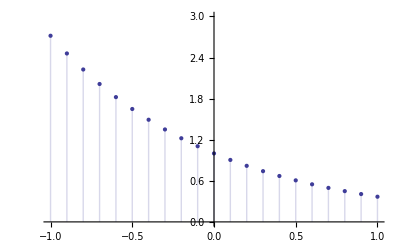

```mathematica
ListPlot[Table[E^(-0.1n),{n,-10,10}],Filling->Axis,DataRange->{-1,1},PlotRange->{0,3}]
```

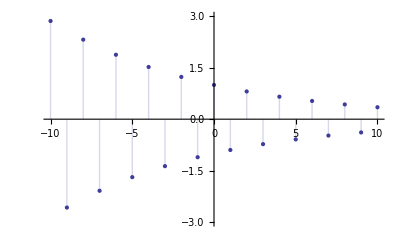

```mathematica
ListPlot[Table[(-0.9)^n,{n,-10,10}],Filling->Axis,DataRange->{-10,10},PlotRange->{-3,3}]
```

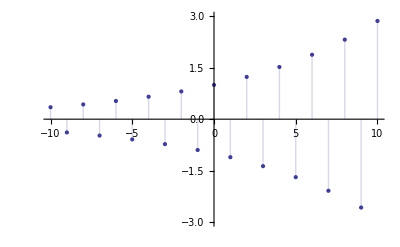

```mathematica
ListPlot[Table[(-0.9)^(-n),{n,-10,10}],Filling->Axis,DataRange->{-10,10},PlotRange->{-3,3}]
```

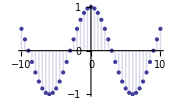

```mathematica
ListPlot[Table[Cos[2π n/12],{n,-10,10,0.5}],DataRange->{-10,10},Filling->Axis]
```

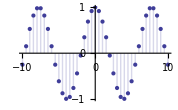

```mathematica
ListPlot[Table[Cos[8π n/31],{n,-10,10,0.5}],DataRange->{-10,10},Filling->Axis]
```

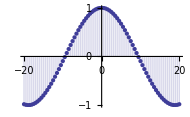

```mathematica
ListPlot[Table[Cos[n/6],{n,-20,20,0.5}],DataRange->{-20,20},Filling->Axis]
```